## Samip Karki π Project

In this class, we have learned many different ways to get approximations of π. In this project, I compare the effectiveness of 3 π algorithms: The Stormer’s Inverse Tangent Method, The Ramanujan’s Series, and the Salamin-Brent Algorithm. For each of these methods, I will find how long it takes to compute 10^12 digits.

In order to do this, I will need to know 2 relationships for each method: the accuracy of the nth iteration and the time it takes to do n iterations. With this information, we can figure out how long it takes to calculate x digits of π. 

Some notes:
For the timing calculation, I will include the time it takes to change the exact arithmetic to high precision because for some methods, because getting a numerical from the exact arithmetic can be a long process (sometimes longer than the algorithms themselves).

### Stormer’s Method

```mathematica
storms[nMax_]:=Module[{sum=0},
Do[sum=sum+44(-1)^(n+1)(1/57)^(2n-1)/(2n-1)+7(-1)^(n+1)(1/239)^(2n-1)/(2n-1)-12(-1)^(n+1)(1/682)^(2n-1)/(2n-1)+24(-1)^(n+1)(1/12943)^(2n-1)/(2n-1),{n,1,nMax}];
4 sum(*returning sum*)]
```

I am getting a list of the the accuracy (number of correct digits of pi) of the nth iteration of the Stormer’s method for n between 1 and 50.

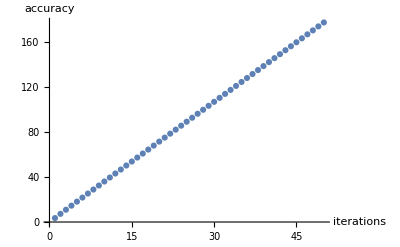

```mathematica
stormvalues= Table[storms[n],{n,1,50}];
stormacc=-Log10[Abs[Pi-N[stormvalues,200]]];(*Need to make sure the N precision is larger than the accuracy of the largest storms iteration*)
ListPlot[stormacc,AxesLabel-> {"iterations","accuracy"},PlotRange->All]
```

Above is a plot of the accuracy of each iteration.

```mathematica
staccfitpoints=Transpose[{Range[Length[stormvalues]],N[stormacc,5]}]; (*x y coordinations of (iteration, accuracy)*)
```

```mathematica
stormfit=LinearModelFit[staccfitpoints,n,n]["BestFit"]
```

0.53576+3.5346 n

The equation above is the line of best fit for accuracy as a function of n.

Below is the calculation for how much time it takes for the nth iteration. I need to take a sample of very large n so that I can get a relationship which I can extrapolate even farther. I use ClearSystemCache inside the table so that calculations are not saved within Mathematica.

```mathematica
precisionst[n_]:=Ceiling[(0.53576+3.5346n)1.20] (*This function gives back a whole number that is greater than the number of digits of accuracy that n iterations will give me. So I can use this to choose a reasonable number of digits in the N[...] function, for a given n*)
```

```mathematica
sttimes=Table[ClearSystemCache[];
Timing[N[storms[n],precisionst[n]]][[1]]
,{n,1,4000,200}];(*Timing table, note that N is taken right after the storms function is called so that I am keeping track of how long the N takes too. Note that the number of digits for N is dependent on n.*)
```

```mathematica
sttimepoints=Transpose[{Table[n,{n,1,4000,200}],N[sttimes,5]}];(*I am making coordinates of the times, so {x=interation, y=time), this way it will be easier to make the ListPlot*)
```

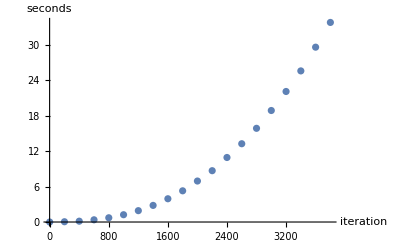

```mathematica
ListPlot[sttimepoints,AxesLabel->{"iteration","seconds"}]
```

The plot above is clearly not linear. It may be time=n^k, so in order to get an equation that best fits this line, I can transform my data by applying Log[ ] to both the x and y coordinates. If this is a n^kgraph, then k will appear as the slope of transformed plot. To explain this another way, consider the following arithmetic:

y = x^k
Log[y] = Log[x^k]
Log[y] = k Log[x]

Here, by plotting the coordinates Log[x] and Log[y], I should get a linear plot.

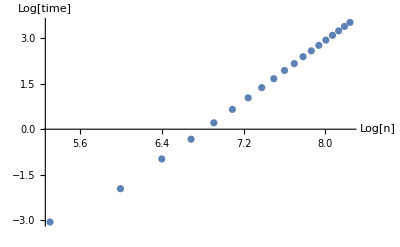

```mathematica
sttimes2=Transpose[{Log[Table[n,{n,1,4000,200}]],N[Log[sttimes],5]}];
ListPlot[sttimes2,AxesLabel->{"Log[n]","Log[time]"}]
```

```mathematica
sttimes2[[1]]
```

{0,Indeterminate}

```mathematica
cleansttimes2=Delete[Delete[sttimes2,1],1]; (*I'm deleting the first two entries (which have Indeterminate) in this list so I can find the best fit line*)
```

```mathematica
fitsttimes2=LinearModelFit[cleansttimes2,logn,logn]["BestFit"] (*This equation solve Log[times] = -16.6872 + 2.44984 Log[n]*)
```

-16.6872+2.44984 logn

```mathematica
bestfitsttimes= Exp[-16.6872+2.44984Log[n]];(*This is the equations that best fits the data for time as a function of iteration for storm method*)
```

Above is the equation of the best fit curve for time as a function of iteration fo the Stormer’s method. Below I show both the data points and the curve. You can see it fits quite well!

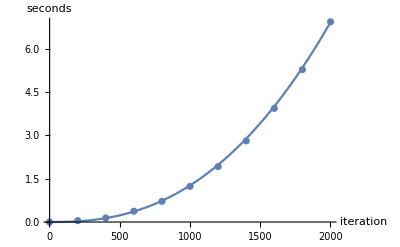

```mathematica
Show[
Plot[bestfitsttimes,{n,1,2000}],
ListPlot[sttimepoints]
,AxesLabel->{"iteration","seconds"}]
```

#### Now we have everything to calculate the time it takes to get 10^12 digits! First, how many iterations are needed for 10^12digits of accuracy?

```mathematica
Solve[10^12==0.53576+3.5346n,n]
```

{{n→2.82917×10^11}}

#### It would take n= 2.82917 e11 iterations. How long does it take to do this many iterations?

```mathematica
Exp[-16.6872+2.44984Log[2.82917 10^11]]/(60 60 24 365)(*Dividing by 60s, 60mins, 24hrs, and 365 days*)
```

2.03595×10^13

#### It would take 2.04 x10^13 years with the Stormer Method!

### Ramanujan’s Series

```mathematica
ramanuj[nMax_]:=Module[{sum=0},
Do[sum=sum+Factorial[4n](1103+26390 n)/((n!)^4(396)^(4n)),{n,0,nMax-1}];
9801/(2 √2 sum)(*returning sum*)](*Module for Ramanujan's series*)
```

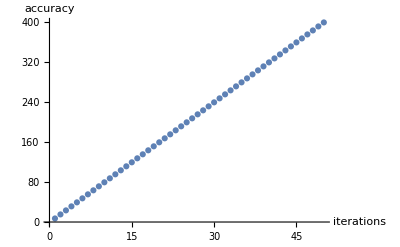

```mathematica
ramvalues= Table[ramanuj[n],{n,1,50}];
ramacc=-Log10[Abs[Pi-N[ramvalues,1000]]];
ListPlot[ramacc,AxesLabel-> {"iterations","accuracy"},PlotRange->All](*1000 digits of approximations*)
```

Above plots the accuracy of each iteration of the Ramanujan Series. We can see it has a clear linear relationship.

```mathematica
ramfitpoints=Transpose[{Range[Length[ramvalues]],N[ramacc,5]}]; 
ramfit=LinearModelFit[ramfitpoints,n,n]["BestFit"]
```

-0.61303+7.9939 n

Above is the equation of the line that best fits the above plot, that is, this line solves for digits of accuracy given n iterations.

Now I will find the relationship between time and iterations

```mathematica
precisionram[n_]:=Ceiling[(-0.61303+7.9939n)1.20] (*chooses how many digits of N[..] should be used for a given n*)
```

```mathematica
ramtimes=Table[ClearSystemCache[];
Timing[N[ramanuj[n],precisionram[n]]][[1]],
{n,1,8000,400}](*This table keeps track of times for each iteration up to n= 8000, going in steps of 400.*)
```

{0.,0.0625,0.28125,0.78125,1.57813,2.78125,4.46875,6.82813,9.89063,11.9219,15.2813,19.3125,23.75,28.8281,34.9531,41.2344,51.2656,57.,60.7031,68.5781}

List Plot for the raw ramtimes below

```mathematica
ramtimepts=Transpose[
{Table[n,{n,1,8000,400}],
N[ramtimes,5]}]; (*makes coordinates of times, so I can plot correctly*)
```

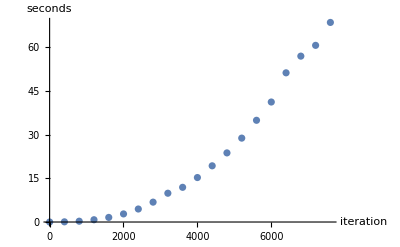

```mathematica
ListPlot[ramtimepts,AxesLabel->{"iteration","seconds"}]
```

Just like before, because this is not linear, I will transform the data by doing Log[x] and Log[y], find the best fit line for the transformed data and then undo the Log to get the equation of the best fit curve.

```mathematica
ramtimepts2=Log[ramtimepts];(*first three entries have indeterminante, so I will delete those*)
```

```mathematica
ramtimepts2=Delete[Delete[Delete[Delete[ramtimepts2,1],1],1],1];
```

```mathematica
ramtimefit=LinearModelFit[ramtimepts2,logn,logn]["BestFit"]
```

-17.3796+2.42508 logn

Above is the equation of the transformed data. I will undo the log and then see how it fits to the original data.

```mathematica
ramtimefit2=Exp[-17.3796+2.42508Log[n]];
```

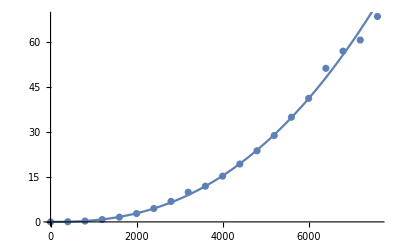

```mathematica
Show[ListPlot[ramtimepts],
Plot[ramtimefit2,{n,1,8000}]
]
```

We have every thing we need to do our calculation.

#### How many iterations are needed to calculate 10^12 digits of pi?

```mathematica
Solve[10^12== -0.61303+7.9939n,n]
```

{{n→1.25095×10^11}}

#### How long will it take to do this many iterations?

```mathematica
Exp[-17.3796+2.42508Log[1.251 10^11]]/(60 60 24 365)
```

7.32936×10^11

#### It will take 7.33 x 10^11 years to calculate one trillion digits with this method!

### Salamin-Brent Algorithm

```mathematica
salamin[nMax_]:=Module[{a=Table[0,nMax],
b=Table[0,nMax],t=Table[0,nMax],p=Table[0,nMax]},
a[[1]]=1; (*Initial conditions*)
b[[1]]=1/(√2);
t[[1]]=1/4;p[[1]]=1;

(*Algorithm*)
Do[a[[n]]=1/2(a[[n-1]]+b[[n-1]]);
b[[n]]=√(a[[n-1]]b[[n-1]]);
t[[n]]=t[[n-1]]-p[[n-1]](a[[n-1]]-a[[n]])^2;
p[[n]]=2p[[n-1]]
,{n,2,nMax}];
(a[[nMax]]+b[[nMax]])^2/(4t[[nMax]])]
```

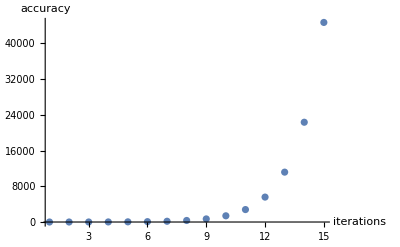

```mathematica
salvalues= Table[salamin[n],{n,1,15}];
salacc=-Log10[Abs[Pi-N[salvalues,60000]]];
ListPlot[salacc,AxesLabel-> {"iterations","accuracy"},PlotRange->All](*1000 digits of approximations*)
```

Above is the plot that shows the digits of accuracy for the first 15 iterations of the Salamin-Brent algorithm. One thing of note is that algorithm does not have a linear relationship. Instead it seems like the accuracy is doubling after each iteration.

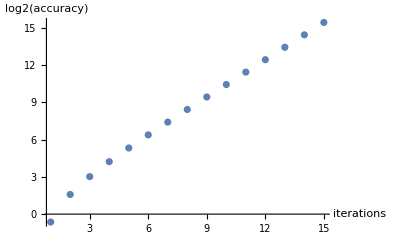

```mathematica
salacc2=Log2[salacc];
ListPlot[salacc2,AxesLabel-> {"iterations","log2(accuracy)"},PlotRange->All]
```

I have transformed the accuracy data by applying Log2[ ] to it to see if I am right about this algorithm doubling after each iteration. Below is the transformed data.

-Graphics-

This looks fairly linear, I can get a line of best fit for this.

```mathematica
salfitpoints=Transpose[{Range[Length[salvalues]],N[salacc2,5]}]; 
salfit=LinearModelFit[salfitpoints,n,n]["BestFit"]
```

-0.47285+1.0831 n

Above is the line of best fit for the transformed accuracy data. Below I have both the points of data and the line of best fit. We can see qualitatively that the line of best fit matches the data well, but not as precisely as the other two π-calculating methods.

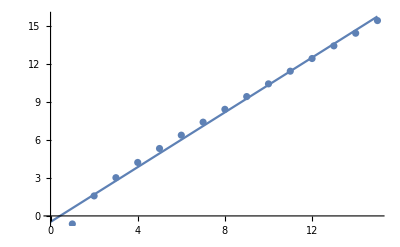

```mathematica
Show[Plot[salfit,{n,0,15}],ListPlot[salacc2]]
```

The line of best fit describes the following Log2[accuracy] = -0.47285 + 1.0831 n
If I take both sides and make them the exponent of 2, I can get an expression for accuracy in terms of n.

```mathematica
salacceq=2^(-0.47285+1.0831n);
```

```mathematica
2^(-0.47285+1.0831(16))
```

118683.

Here, I will do my timing calculations

```mathematica
precisionsal[n_]:=Ceiling[2^(-0.47285+1.0831(1.10)n)(1.10)]
```

```mathematica
ClearSystemCache[]
saltimes=Table[ClearSystemCache[];
Timing[N[salamin[n],precisionsal[n]]][[1]]
,{n,1,18}];(*For salamin brent, it is very important that the precision of N is different for each n, because much of the run is dependent on how many digits of precision are needed.*)
```

```mathematica
saltimes
```

{0.,0.,0.015625,0.,0.,0.,0.,0.015625,0.015625,0.03125,0.15625,0.625,2.07813,9.15625,32.2969,115.,538.406,21581.5}

```mathematica
saltimepts=Transpose[{Table[n,{n,1,18}],
saltimes}];
```

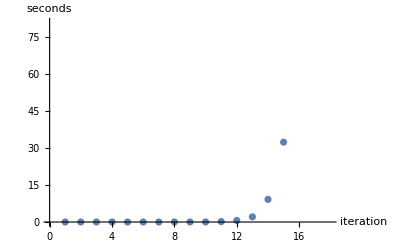

```mathematica
ListPlot[saltimepts,AxesLabel->{"iteration","seconds"}]
```

Like with the other two methods, I will apply log to both the x and y to get a linear relationship for the times.

```mathematica
saltimepts2=Log[saltimepts]; (*I need to get rid of the first 10 points, because they are too small to fit the data well*)
```

```mathematica
saltimepts2=Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[saltimepts2,1],1],1],1],1],1],1],1],1],1]
```

{{Log[11],-1.8563},{Log[12],-0.470004},{Log[13],0.731466},{Log[14],2.21444},{Log[15],3.47497},{Log[16],4.74493},{Log[17],6.28861},{Log[18],9.97959}}

```mathematica
saltimefit=LinearModelFit[saltimepts2,logn,logn]["BestFit"]
```

-54.8533+21.7901 logn

Undo the log

```mathematica
saltimeeq=Exp[-54.8533+21.7901Log[n]];
```

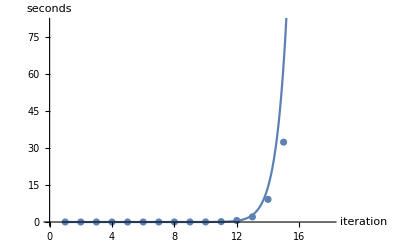

```mathematica
Show[ListPlot[saltimepts,AxesLabel->{"iteration","seconds"}],
Plot[saltimeeq,{n,1,18}],AxesLabel->{"iteration","seconds"}]
```

Above shows the curve of best fit with the time data points from saltimes.

#### How many iterations are needed for 10^12 digits of accuracy:

```mathematica
Solve[10^12==2^(-0.47285+1.081n),n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→37.3136}}

How long does it take to do this many iterations?

```mathematica
Exp[-54.8533+21.7901Log[37.3136]]/(60 60 24 365)
```

850.845

#### It would only take 851 years with the Salamin-Brent Algorithm!

## Conclusion

Comparision of each algorithm
How long does it take to compute 10^12digits of π?

1) Salamin-Brent Algorithm
	851 years
	
2) Ramanujan’s Series
	7.33 x 10^11 years

3) Stormer’s Method
	2.04x 10^13